```mathematica
(*Function to compute the Liouville operator for XX-YY coupling*)liouv2qXXYY[x0_]:=Module[{v},v=ConstantArray[0,4^2];
v[[FromDigits[Mod[x0+{1,1,0,0},2],2]+1]]-=I;
v[[FromDigits[Mod[x0+{0,0,1,1},2],2]+1]]+=I;
v[[FromDigits[Mod[x0+{1,1,0,0},2],2]+1]]+=(-1)^(Mod[x0[[1]]+x0[[2]]+1,2]);
v[[FromDigits[Mod[x0+{0,0,1,1},2],2]+1]]+=(-1)^(Mod[x0[[3]]+x0[[4]]+1,2]);
v]
```

```mathematica
(*Function to compute the dissipation operator*)
Diss2qTLC[x0_]:=Module[{v},v=ConstantArray[0,4^2];
v[[FromDigits[x0,2]+1]]-=2;
(*for X rho X*)v[[FromDigits[Mod[x0+{0,1,0,1},2],2]+1]]+=1;
(*for Y rho Y*)v[[FromDigits[Mod[x0+{0,1,0,1},2],2]+1]]+=(-1)^(x0[[2]]+x0[[4]]);
(*for Z rho Z*)v[[FromDigits[x0,2]+1]]+=((-1)^(x0[[2]]+x0[[4]])-1);
v]
```

```mathematica
(*Function to compute the superoperator*)
Superop6[x0_,alpha_,gamma_]:=alpha*liouv2qXXYY[x0]+gamma*Diss2qTLC[x0]

(*Function to compute the matrix representation of the superoperator*)
MatrSuperOp6[alpha_,gamma_]:=Module[{mat},mat=ConstantArray[0,{4^2,4^2}];
Do[mat[[All,i+1]]=Superop6[IntegerDigits[i,2,4],alpha,gamma],{i,0,4^2-1}];
Transpose[mat]]
```

```mathematica
(*Example usage*)
MatrSuperOp6[α,γ]//MatrixForm

NullSpace[MatrSuperOp6[α,γ]]
```

(-2 γ | 0 | 0 | (-1+ⅈ) α | 0 | 2 γ | 0 | 0 | 0 | 0 | 0 | 0 | (-1-ⅈ) α | 0 | 0 | 0
0 | -4 γ | (1+ⅈ) α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1-ⅈ) α | 0 | 0
0 | (1+ⅈ) α | -2 γ | 0 | 0 | 0 | 0 | 2 γ | 0 | 0 | 0 | 0 | 0 | 0 | (-1-ⅈ) α | 0
(-1+ⅈ) α | 0 | 0 | -4 γ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1-ⅈ) α
0 | 0 | 0 | 0 | -4 γ | 0 | 0 | (-1+ⅈ) α | (1-ⅈ) α | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 γ | 0 | 0 | 0 | 0 | -2 γ | (1+ⅈ) α | 0 | 0 | (1-ⅈ) α | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | (1+ⅈ) α | -4 γ | 0 | 0 | 0 | (1-ⅈ) α | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 γ | 0 | (-1+ⅈ) α | 0 | 0 | -2 γ | 0 | 0 | 0 | (1-ⅈ) α | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (1-ⅈ) α | 0 | 0 | 0 | -2 γ | 0 | 0 | (-1+ⅈ) α | 0 | 2 γ | 0 | 0
0 | 0 | 0 | 0 | 0 | (1-ⅈ) α | 0 | 0 | 0 | -4 γ | (1+ⅈ) α | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | (1-ⅈ) α | 0 | 0 | (1+ⅈ) α | -2 γ | 0 | 0 | 0 | 0 | 2 γ
0 | 0 | 0 | 0 | 0 | 0 | 0 | (1-ⅈ) α | (-1+ⅈ) α | 0 | 0 | -4 γ | 0 | 0 | 0 | 0
(-1-ⅈ) α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 γ | 0 | 0 | (-1+ⅈ) α
0 | (-1-ⅈ) α | 0 | 0 | 0 | 0 | 0 | 0 | 2 γ | 0 | 0 | 0 | 0 | -2 γ | (1+ⅈ) α | 0
0 | 0 | (-1-ⅈ) α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (1+ⅈ) α | -4 γ | 0
0 | 0 | 0 | (-1-ⅈ) α | 0 | 0 | 0 | 0 | 0 | 0 | 2 γ | 0 | (-1+ⅈ) α | 0 | 0 | -2 γ)

{{0,0,1,0,0,0,0,1,1,0,0,0,0,1,0,0}}

```mathematica
Eigenvalues[MatrSuperOp6[α,γ]]
```

{0,2 (α-2 γ),-2 ⅈ (α-2 ⅈ γ),2 ⅈ (α+2 ⅈ γ),-4 γ,-4 γ,-4 γ,-2 (α+2 γ),(1+ⅈ) ((-1+ⅈ) γ-√2 √(-ⅈ α^2-ⅈ γ^2)),(1+ⅈ) ((-1+ⅈ) γ+√2 √(-ⅈ α^2-ⅈ γ^2)),(1+ⅈ) ((-1+ⅈ) γ-√2 √(ⅈ α^2-ⅈ γ^2)),(1+ⅈ) ((-1+ⅈ) γ+√2 √(ⅈ α^2-ⅈ γ^2)),(1+ⅈ) Root[-16 α^4-(16+16 ⅈ) γ^3 #1-24 ⅈ γ^2 #1^2+(6-6 ⅈ) γ #1^3+#1^4&,1],(1+ⅈ) Root[-16 α^4-(16+16 ⅈ) γ^3 #1-24 ⅈ γ^2 #1^2+(6-6 ⅈ) γ #1^3+#1^4&,2],(1+ⅈ) Root[-16 α^4-(16+16 ⅈ) γ^3 #1-24 ⅈ γ^2 #1^2+(6-6 ⅈ) γ #1^3+#1^4&,3],(1+ⅈ) Root[-16 α^4-(16+16 ⅈ) γ^3 #1-24 ⅈ γ^2 #1^2+(6-6 ⅈ) γ #1^3+#1^4&,4]}

```mathematica
FromDigits[Mod[{0,1,0,1},2],2]
```

5

## TCL reinvented

First let' s going to create the code for commutator and anticommutator. 
[A,B]=AB-BA      {A,B}=AB+BA
As an example [X,X]=0 and [X,Y]=2iZ

```mathematica
Commut[A_,B_]:=A.B-B.A
Anticommut[A_,B_]:=A.B+B.A
Commut[PauliMatrix[1],PauliMatrix[1]]
Commut[PauliMatrix[1],PauliMatrix[2]]
```

{{0,0},{0,0}}

{{2 ⅈ,0},{0,-2 ⅈ}}

In general for a 2x2 matrix

```mathematica
Commut[{{a,b},{c,d}},{{α,β},{γ,δ}}]
Anticommut[{{a,b},{c,d}},{{α,β},{γ,δ}}]
```

{{-c β+b γ,-b α+a β-d β+b δ},{c α-a γ+d γ-c δ,c β-b γ}}

{{2 a α+c β+b γ,b α+a β+d β+b δ},{c α+a γ+d γ+c δ,c β+b γ+2 d δ}}

Here we construct S(t)=ⅇ^(ⅈ t Ω)σ+  + ⅇ^(-ⅈ t Ω) σ-

```mathematica
St[plus_,minus_]:={{0,minus},{plus, 0}}
St[Exp[I c t],Exp[-I d t]]//MatrixForm
Clear[SΩt,rho,ρ11,ρ01,ρ10,t0]
SΩt[t_]:=St[Exp[I Ω t],Exp[-I Ω t]]
rho={{1-ρ11,ρ01},{ρ10,ρ11}};
SΩt[t0]//MatrixForm
```

(0 | ⅇ^(-ⅈ d t)
ⅇ^(ⅈ c t) | 0)

(0 | ⅇ^(-ⅈ t0 Ω)
ⅇ^(ⅈ t0 Ω) | 0)

### For TCL2

For K2 we have ν [0,[1,ρ]] + iη[0,{1,ρ}]

```mathematica
Clear[t0,t1,ν,η]
```

```mathematica
FullSimplify[ν Commut[SΩt[t0],Commut[SΩt[t1],rho]]+I η Commut[SΩt[t0],Anticommut[SΩt[t1],rho]]]//MatrixForm
```

(2 ν (1-2 ρ11) Cos[(t0-t1) Ω]+2 η Sin[(t0-t1) Ω] | 2 ⅇ^(-ⅈ (t0+t1) Ω) ν (ⅇ^(2 ⅈ t1 Ω) ρ01-ρ10)
-2 ⅇ^(ⅈ (t0-t1) Ω) ν (ⅇ^(2 ⅈ t1 Ω) ρ01-ρ10) | 2 ν (-1+2 ρ11) Cos[(t0-t1) Ω]-2 η Sin[(t0-t1) Ω])

```mathematica
rho
```

{{1-ρ11,ρ01},{ρ10,ρ11}}

Now lets apply it to the bath spectral density of Drude Lorentz to compare it with the python notebook

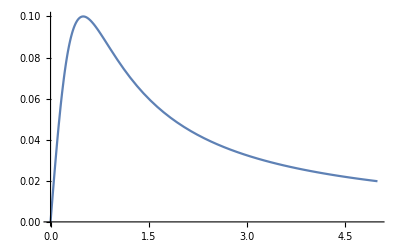

```mathematica
JDLnew[ω_, λ_,γ_]:=((2ω γ λ)/(ω^2+γ^2))
γp=0.5; (*γ is like a cutoof frequency*)
λp=0.1; (* λ is the coupling constant*)
Tp=1;(*temperature*)
Plot[JDLnew[ω, λp,γp],{ω,0,5}]
```

The Markov decay rate is simply 2πJ(Ω)Coth[βΩ/2]. Check there is a factor of 1/π in the J(ω) spectral density

```mathematica
γMarkovDL[α_,β_,λ_,γ_]:=2π( JDLnew[α, λ,γ]/π)Coth[β α/2]
```

According to the TCL2 expression D[ρ11,t]=γ+(t)-γ(t)ρ11 where 
ν[τ]=∫_0^Infty ⅆω J[ω]Coth[βω/2]Cos[ω τ]
η[τ]=-∫_0^Infty ⅆω J[ω]Sin[ω τ]
γ(t)=4∫_0^t ⅆτ ν[τ]Cos[Ωτ]= 2∫_0^Infty ⅆω J[ω]Coth[βω/2](Sin[(ω+Ω)t]/(ω+Ω)+Sin[(-ω+Ω)t]/(-ω+Ω))
=2∫_-Infty^Infty ⅆω J[ω]Coth[βω/2](Sin[(ω+Ω)t]/(ω+Ω))

```mathematica
Integrate[Cos[a t]Cos[b t],{t,0,t}]
Integrate[Sin[a t]Sin[b t],{t,0,t}]
```

(a Cos[b t] Sin[a t]-b Cos[a t] Sin[b t])/(a^2-b^2)

(b Cos[b t] Sin[a t]-a Cos[a t] Sin[b t])/(a^2-b^2)

```mathematica
γBRDL[t_,β_,λ_,γ_]:=2 NIntegrate[JDLnew[u, λ,γ]/π Coth[β u/2](Sin[(u+1)t]/(u+1)+Sin[(1-u)t]/(1-u)),{u,0,Infinity}]
γBRDLComplete[t_,β_,λ_,γ_]:=2 NIntegrate[JDLnew[u, λ,γ]/π Coth[β u/2](Sin[(u+1)t]/(u+1)),{u,-Infinity,Infinity}]
γBRDLInComplete[t_,β_,λ_,γ_]:=4 NIntegrate[JDLnew[u, λ,γ]/π Coth[β u/2](Sin[(u+1)t]/(u+1)),{u,0,Infinity}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.81037×10^7}. NIntegrate obtained 0.000341373 and 8.61907×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {-4.81037×10^7}. NIntegrate obtained 0.000341373 and 8.61907×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.81037×10^7}. NIntegrate obtained 0.000170682 and 4.30787×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

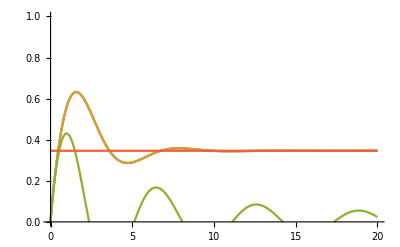

```mathematica
Plot[{γBRDL[t,1/Tp,λp,γp],γBRDLComplete[t,1/Tp,λp,γp],γBRDLInComplete[t,1/Tp,λp,γp],γMarkovDL[1,1/Tp,λp,γp]},{t,0,20},PlotRange->{0,1}]
```

```mathematica
AbsoluteTiming[γBRDL[0.2,1/Tp,λp,γp]]
AbsoluteTiming[γBRDLComplete[0.2,1/Tp,λp,γp]]
AbsoluteTiming[2γBRDLInComplete[0.2,1/Tp,λp,γp]]
```

{0.03531,0.175212}

{0.030548,0.175212}

{0.011707,0.170796}

Now lets find γPlus 
ν[τ]=∫_0^Infty ⅆω J[ω]Coth[βω/2]Cos[ω τ]
η[τ]= -∫_0^Infty ⅆω J[ω]Sin[ω τ]
γ+(t)=4∫_0^t ⅆτ (ν[τ]Cos[Ωτ]+η[τ]Sin[Ωτ])= 2∫_0^Infty ⅆω J[ω](2/(Exp[βω]-1)Sin[(-ω+Ω)t]/(-ω+Ω)+2/(1-Exp[-βω])Sin[(ω+Ω)t]/(ω+Ω))=2∫_0^Infty ⅆω J[ω](2/(1-Exp[-βω])Sin[(ω+Ω)t]/(ω+Ω))

0.0857405

0.0857405

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.81037×10^7}. NIntegrate obtained 0.000170682 and 4.30787×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.81037×10^7}. NIntegrate obtained 0.000170682 and 4.87139×10^-8 for the integral and error estimates.

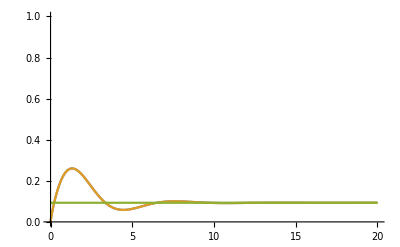

```mathematica
γPlusMarkovDL[α_,β_,λ_,γ_]:=2π( JDLnew[α, λ,γ]/π)Exp[-β α]/(1-Exp[-β α])
γPlusBRDL[t_,β_,λ_,γ_]:=2 NIntegrate[JDLnew[u, λ,γ]/π 1/(1-Exp[-β u])(Sin[(u+1)t]/(u+1)+Sin[(1-u)t]/(1-u)Exp[-β u]),{u,0,Infinity}]
γPlusBRDLComplete[t_,β_,λ_,γ_]:=2 NIntegrate[JDLnew[u, λ,γ]/π 1/(1-Exp[-β u])Sin[(u+1)t]/(u+1),{u,-Infinity,Infinity}]
γPlusBRDL[0.2,1/Tp,λp,γp]
γPlusBRDLComplete[0.2,1/Tp,λp,γp]
Plot[{γPlusBRDL[t,1/Tp,λp,γp],γPlusBRDLComplete[t,1/Tp,λp,γp],γPlusMarkovDL[1,1/Tp,λp,γp]},{t,0,20},PlotRange->{0,1}]
```

Check the timing to get faster restult

```mathematica
AbsoluteTiming[γPlusBRDL[0.2,1/Tp,λp,γp]]
AbsoluteTiming[γPlusBRDLComplete[0.2,1/Tp,λp,γp]]
```

{0.030415,0.0857405}

{0.022904,0.0857405}

Now we are solving the complete solution for ρ11 :  ρ11 Exp[-]

```mathematica
Clear[int1,int2,int2BRDL]
int1[tp_?NumericQ,β_,λ_,γ_]:=int1[tp,β,λ,γ]=NIntegrate[γBRDLComplete[tpp,β,λ,γ],{tpp,0,tp}]

int2[t_?NumericQ,β_,λ_,γ_]:=int2[t,β,λ,γ]=NIntegrate[γPlusBRDLComplete[tp,β,λ,γ]Exp[int1[tp,β,λ,γ]],{tp,0.05,t}]
(*NIntegrate[γPlusBRDL[tp,β,λ,γ]Exp[int1BRDL[tp,β,λ,γ]]*)
ρ11TCL2DL[t_,ρ0_,β_,λ_,γ_]:=Exp[-int1[t,β,λ,γ]](ρ0+int2[t,β,λ,γ])
```

```mathematica
ρ11TCL2DL[1,0,βp,λp,γp]
```

0.132447

NIntegrate::inumr: The integrand (0.031831 u Sin[tp (1+u)])/((1-ⅇ^-u) (1+u) (0.25+u^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{{0.04,1.00024},{0.54,0.947833},{1.04,0.860651},{1.54,0.78654},{2.04,0.740766},{2.54,0.720012},{3.04,0.716148},{3.54,0.721777},{4.04,0.731226},{4.54,0.740435}}

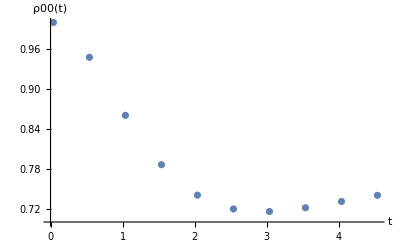

```mathematica
ρ0p=0;
βp=1/Tp;
γp=0.5;
λp=0.1;

TABLEρ00BRDL=Table[{t,1-ρ11TCL2DL[t,ρ0p,βp,λp,γp]},{t,0.04,5,0.5}]
ListPlot[TABLEρ00BRDL,AxesLabel->{"t","ρ00(t)"}]
```

```mathematica
TABLEρ00BRDL
```

{{0.04,1.00024},{0.54,0.947833},{1.04,0.860651},{1.54,0.78654},{2.04,0.740766},{2.54,0.720012},{3.04,0.716148},{3.54,0.721777},{4.04,0.731226},{4.54,0.740435}}

### For TCL4

For K4 we have 

ν02 ν13 [0, [[1,2],[3, ρ]]]+I ν02 η13  [0, [[1, 2], {3, ρ}]]
 [0, [[1,2],[3, ρ]]]

```mathematica
FullSimplify[Commut[SΩt[t],Commut[Commut[SΩt[t1],SΩt[t2]],Commut[SΩt[t3],rho]]]]//MatrixForm
```

(8 (1-2 ρ11) Sin[(t1-t2) Ω] Sin[(t-t3) Ω] | 0
0 | 8 (-1+2 ρ11) Sin[(t1-t2) Ω] Sin[(t-t3) Ω])

[0, [[1, 2], {3, ρ}]]

```mathematica
FullSimplify[Commut[SΩt[t],Commut[Commut[SΩt[t1],SΩt[t2]],Anticommut[SΩt[t3],rho]]]]//MatrixForm
```

(8 ⅈ Cos[(t-t3) Ω] Sin[(t1-t2) Ω] | 0
0 | -8 ⅈ Cos[(t-t3) Ω] Sin[(t1-t2) Ω])

I η02 ν13 [0, {[1, 2], [3, ρ]}] - η02 η13 [0, {[1, 2], {3, ρ}}]
 [0, {[1, 2], [3, ρ]}]

```mathematica
FullSimplify[Commut[SΩt[t],Anticommut[Commut[SΩt[t1],SΩt[t2]],Commut[SΩt[t3],rho]]]]
```

{{0,0},{0,0}}

[0, {[1, 2], {3, ρ}}]

```mathematica
FullSimplify[Commut[SΩt[t],Anticommut[Commut[SΩt[t1],SΩt[t2]],Anticommut[SΩt[t3],rho]]]]//MatrixForm
```

(0 | 4 ⅇ^(-ⅈ (t+t1+t2+t3) Ω) (ⅇ^(2 ⅈ t1 Ω)-ⅇ^(2 ⅈ t2 Ω)) (ⅇ^(2 ⅈ t3 Ω) ρ01+ρ10)
4 ⅇ^(ⅈ (t-t1-t2-t3) Ω) (-ⅇ^(2 ⅈ t1 Ω)+ⅇ^(2 ⅈ t2 Ω)) (ⅇ^(2 ⅈ t3 Ω) ρ01+ρ10) | 0)

ν03 ν12  [0, [[1,3],[2,ρ]]] + I ν03 η12 [0, [[1, 3], {2, ρ} ]]
 [0, [[1,3],[2,ρ]]]

```mathematica
FullSimplify[Commut[SΩt[t],Commut[Commut[SΩt[t1],SΩt[t3]],Commut[SΩt[t2],rho]]]]//MatrixForm
```

(8 (1-2 ρ11) Sin[(t-t2) Ω] Sin[(t1-t3) Ω] | 0
0 | 8 (-1+2 ρ11) Sin[(t-t2) Ω] Sin[(t1-t3) Ω])

[0, [[1, 3], {2, ρ} ]]

```mathematica
FullSimplify[Commut[SΩt[t],Commut[Commut[SΩt[t1],SΩt[t3]],Anticommut[SΩt[t2],rho]]]]//MatrixForm
```

(8 ⅈ Cos[(t-t2) Ω] Sin[(t1-t3) Ω] | 0
0 | -8 ⅈ Cos[(t-t2) Ω] Sin[(t1-t3) Ω])

Iη03 ν12 [0, {[1, 3], [2, ρ]}]- η03 η12 [0, {[1, 3], {2, ρ}}]
 [0, {[1, 3], [2, ρ]}]

```mathematica
FullSimplify[Commut[SΩt[t],Anticommut[Commut[SΩt[t1],SΩt[t3]],Commut[SΩt[t2],rho]]]]
```

{{0,0},{0,0}}

[0, {[1, 3], {2, ρ}}]

```mathematica
FullSimplify[Commut[SΩt[t],Anticommut[Commut[SΩt[t1],SΩt[t3]],Anticommut[SΩt[t2],rho]]]]//MatrixForm
```

(0 | 4 ⅇ^(-ⅈ (t+t1+t2+t3) Ω) (ⅇ^(2 ⅈ t1 Ω)-ⅇ^(2 ⅈ t3 Ω)) (ⅇ^(2 ⅈ t2 Ω) ρ01+ρ10)
4 ⅇ^(ⅈ (t-t1-t2-t3) Ω) (-ⅇ^(2 ⅈ t1 Ω)+ⅇ^(2 ⅈ t3 Ω)) (ⅇ^(2 ⅈ t2 Ω) ρ01+ρ10) | 0)

[0, [1, [[2,3] ρ]]]

```mathematica
FullSimplify[Commut[SΩt[t],Commut[SΩt[t1],Commut[Commut[SΩt[t2],SΩt[t3]],rho]]]]//MatrixForm
```

(0 | 4 ⅇ^(-ⅈ (t+t1+t2+t3) Ω) (-ⅇ^(2 ⅈ t2 Ω)+ⅇ^(2 ⅈ t3 Ω)) (ⅇ^(2 ⅈ t1 Ω) ρ01+ρ10)
4 ⅇ^(ⅈ (t-t1-t2-t3) Ω) (ⅇ^(2 ⅈ t2 Ω)-ⅇ^(2 ⅈ t3 Ω)) (ⅇ^(2 ⅈ t1 Ω) ρ01+ρ10) | 0)

[0, [1, {[2, 3] ,ρ}]]

```mathematica
FullSimplify[Commut[SΩt[t],Commut[SΩt[t1],Anticommut[Commut[SΩt[t2],SΩt[t3]],rho]]]]//MatrixForm
```

(-8 ⅈ Cos[(t-t1) Ω] Sin[(t2-t3) Ω] | 0
0 | 8 ⅈ Cos[(t-t1) Ω] Sin[(t2-t3) Ω])

#### Let’s going to analize

γ4 = 16(ν02 ν13 s12 s03 + ν03 ν12 s13 s02)

```mathematica
Integrate[Cos[ω(t1-t3)]Sin[ω(t-t3)],{t3,0,t}]
```

(Cos[(-t+t1) ω]-Cos[(t+t1) ω]+2 t ω Sin[(t-t1) ω])/(4 ω)

```mathematica
FullSimplify[Integrate[Cos[ω(t1-t3)]Sin[Ω(t-t3)],{t3,0,t2}]]
```

(Cos[t1 ω-t Ω]-Cos[t1 ω-t2 ω-t Ω+t2 Ω])/(2 ω-2 Ω)+(Sin[1/2 t2 (ω+Ω)] Sin[t1 ω+t Ω-1/2 t2 (ω+Ω)])/(ω+Ω)

```mathematica
FullSimplify[Integrate[Sin[ω(t1-t3)]Cos[(t-t3)],{t3,0,t2}]]
```

-(Sin[1/2 t2 (-1+ω)] Sin[t+1/2 t2 (-1+ω)-t1 ω])/(-1+ω)+(Sin[1/2 t2 (1+ω)] Sin[t+t1 ω-1/2 t2 (1+ω)])/(1+ω)

```mathematica
FullSimplify[Integrate[Integrate[Cos[ωp(t-t2)]Sin[Ω(t1-t2)]Integrate[Cos[ω(t1-t3)]Sin[Ω(t-t3)],{t3,0,t2}],{t2,0,t1}],{t1,0,t}]]
```

$Aborted

```mathematica
FullSimplify[Integrate[Cos[ω(t1-t3)]Sin[Ω(t-t3)],{t3,0,t2}]]
```

(Cos[t1 ω-t Ω]-Cos[t1 ω-t2 ω-t Ω+t2 Ω])/(2 ω-2 Ω)+(Sin[1/2 t2 (ω+Ω)] Sin[t1 ω+t Ω-1/2 t2 (ω+Ω)])/(ω+Ω)

```mathematica
FullSimplify[Integrate[Cos[ω(t1-t3)]Sin[(t-t3)],{t3,0,t2}]]
```

(Sin[1/2 t2 (-1+ω)] Sin[t+1/2 t2 (-1+ω)-t1 ω])/(-1+ω)+(Sin[1/2 t2 (1+ω)] Sin[t+t1 ω-1/2 t2 (1+ω)])/(1+ω)

```mathematica
FullSimplify[Integrate[Cos[ω(t-t3)]Sin[(t1-t3)],{t3,0,t2}]]
```

(Sin[1/2 t2 (-1+ω)] Sin[t1+1/2 t2 (-1+ω)-t ω])/(-1+ω)+(Sin[1/2 t2 (1+ω)] Sin[t1+t ω-1/2 t2 (1+ω)])/(1+ω)

Checking that integrating over positive frequencies is equivalent to integrate over all possible frequencies.

```mathematica
JDLnew[ω_, λ_,γ_]:=((2ω γ λ)/(ω^2+γ^2))
gamma4approx[t_,t1_,t2_,β_, λ_,γ_]:=NIntegrate[JDLnew[ω, λ,γ]/π Coth[β ω/2]((Sin[1/2 t2 (-1+ω)] Sin[t+1/2 t2 (-1+ω)-t1 ω])/(-1+ω)+(Sin[1/2 t2 (1+ω)] Sin[t+t1 ω-1/2 t2 (1+ω)])/(1+ω)),{ω,0,Infinity}]
gamma4approxmitad[t_,t1_,t2_,β_, λ_,γ_]:= NIntegrate[JDLnew[ω, λ,γ]/π Coth[β ω/2]((Sin[1/2 t2 (1+ω)] Sin[t+t1 ω-1/2 t2 (1+ω)])/(1+ω)),{ω,-Infinity,Infinity}]
gamma4approx[1,2,1,1/Tp, λp,γp]
gamma4approxmitad[1,2,1,1/Tp, λp,γp]
```

0.0396322

0.0396322

g1=@(t,t1,t2, beta, lambda, gamma,Msup) integral(@(u) (JDLnew(u, lambda, gamma) ./ pi) .* coth(beta * u/ 2) .* integrand1(u, t,t1,t2) ,-Msup,Msup,’ArrayValued’,true, ‘RelTol’, 1e-1, ‘AbsTol’, 1e-1)

nu02 = @(t, t2, beta, lambda, gamma, Msup) integral (@(omega) (JDLnew (omega, lambda, gamma) ./pi) .*coth (beta*omega/2) .*cos (omega .*(t - t2)), 0, Msup, ' ArrayValued', true, ' RelTol', 1 e - 1, ' AbsTol', 1 e - 1)
%alpha1 = @(t,beta, lambda, gamma,Msup) integral(@(t1) integral(@(t2) nu02(t,t2, beta, lambda, gamma,Msup).*sin(t1-t2).*g1(t,t1,t2, beta, lambda, gamma,Msup) ,0,t1,’ArrayValued’,true,’RelTol’, 1e-1, ‘AbsTol’, 1e-1),0,t,’ArrayValued’,true, ‘AbsTol’, 1e-1)

```mathematica
Msup=3
g1f[t_,t1_,t2_,β_, λ_,γ_]:= NIntegrate[JDLnew[ω, λ,γ]/π Coth[β ω/2]((Sin[1/2 t2 (1+ω)] Sin[t+t1 ω-1/2 t2 (1+ω)])/(1+ω)),{ω,-Msup,Msup}]
ντ[t_,β_, λ_,γ_]:=NIntegrate[JDLnew[ω, λ,γ]/π Coth[β ω/2]Cos[ω t],{ω,0,Msup}]

alpha1integral1[t_?NumericQ,t1_?NumericQ,β_?NumericQ, λ_?NumericQ,γ_?NumericQ]:=NIntegrate[g1f[t,t1,t2,β, λ,γ]*ντ[t-t2,β, λ,γ]*Sin[t1-t2],{t2,0,t1}]
alpha1integral2[t_?NumericQ,β_?NumericQ, λ_?NumericQ,γ_?NumericQ]:=NIntegrate[alpha1integral1[t,t1,β, λ,γ],{t1,0,t}]
alpha1integral2[6,1/Tp, λp,γp]
```

3

-0.00876564

Si da lo mismo que Matlab, vamos a confiar que estamos bien en gamma

```mathematica
Tp
λp
γp
```

1

0.1

0.5

```mathematica
Clear[funcTodd]
funcTodd2[t_,ω_,ωp_,Ω_]:=Integrate[Integrate[Cos[ω(t-t2)]Sin[Ω(t1-t2)]*Integrate[Cos[ωp(t1-t3)]Sin[Ω(t-t3)],{t3,0,t2}],{t2,0,t1}],{t1,0,t}]
funcTodd2[t,ω,ωp,Ω]
```

-((ω (2 Ω Cos[t Ω]-(Ω+ωp) Cos[t (2 Ω-ωp)]+(-Ω+ωp) Cos[t ωp]) Sin[t ω])/(4 (ω^2-Ω^2) (Ω-ωp)^2 (Ω+ωp)))-(Ω Sin[t (ω-Ω)])/(4 (ω-Ω) (Ω-ωp) (ω+ωp) (ω-2 Ω+ωp))+Sin[t (ω-Ω)]/(8 (ω-Ω) (ω-ωp) (Ω+ωp))-Sin[t (ω-Ω)]/(8 (ω-Ω) (ω-2 Ω-ωp) (Ω+ωp))-(Ω Sin[t (ω+Ω)])/(4 (ω+Ω) (ω-ωp) (Ω-ωp) (ω+2 Ω-ωp))-Sin[t (ω+Ω)]/(8 (ω+Ω) (ω+ωp) (Ω+ωp))+Sin[t (ω+Ω)]/(8 (ω+Ω) (Ω+ωp) (ω+2 Ω+ωp))+(-Sin[t (ω-Ω)]+Sin[t (ω-ωp)])/(8 (ω+Ω) (Ω-ωp) (Ω+ωp))+(-Sin[t (ω-Ω)]+Sin[t (ω-ωp)])/(8 (ω-ωp) (-Ω+ωp) (Ω+ωp))+(-Sin[t (ω+Ω)]+Sin[t (ω-ωp)])/(8 (ω-ωp) (-Ω+ωp) (Ω+ωp))+(Sin[t (ω-Ω)]-Sin[t (ω-2 Ω-ωp)])/(8 (ω-2 Ω-ωp) (Ω+ωp)^2)+(-Sin[t (ω-Ω)]+Sin[t (ω-2 Ω-ωp)])/(8 (ω-Ω) (Ω+ωp)^2)+(Ω (ω Cos[t Ω] Sin[t ω]-ωp Cos[t ω] Sin[t Ω]+ωp Sin[t (Ω-ωp)]))/(2 (ω^2-Ω^2) (ω-ωp) (Ω-ωp) (ω+ωp))+(Sin[t (ω+Ω)]-Sin[t (ω+2 Ω-ωp)])/(8 (Ω-ωp)^2 (ω+2 Ω-ωp))+(Ω Cos[t ω] (-2 ωp Sin[t Ω]+(Ω+ωp) Sin[t (2 Ω-ωp)]+(Ω-ωp) Sin[t ωp]))/(4 (-ω^2+Ω^2) (Ω-ωp)^2 (Ω+ωp))+(Sin[t (ω+Ω)]-Sin[t (ω+ωp)])/(8 (Ω-ωp) (ω+ωp) (Ω+ωp))+(-Sin[t (ω-Ω)]+Sin[t (ω+ωp)])/(8 (ω+ωp) (-Ω^2+ωp^2))+(-Sin[t (ω+Ω)]+Sin[t (ω+ωp)])/(8 (ω-Ω) (Ω-ωp) (Ω+ωp))+(Sin[t (ω-Ω)]-Sin[t (ω-2 Ω+ωp)])/(8 (Ω-ωp)^2 (ω-2 Ω+ωp))+(Sin[t (ω+Ω)]-Sin[t (Ω+ωp)])/(8 (ω-Ω) (ω-ωp) (Ω+ωp))+(Sin[t (ω-Ω)]+Sin[t (Ω+ωp)])/(8 (ω-Ω) (ω+ωp) (Ω+ωp))-(Sin[t (ω-Ω)]+Sin[t (Ω+ωp)])/(8 (ω+Ω) (ω+ωp) (Ω+ωp))+(-Sin[t (ω+Ω)]+Sin[t (Ω+ωp)])/(8 (ω+Ω) (ω-ωp) (Ω+ωp))+(Sin[t (ω+Ω)]-Sin[t (ω+2 Ω+ωp)])/(8 (Ω+ωp)^2 (ω+2 Ω+ωp))+(-Sin[t (ω+Ω)]+Sin[t (ω+2 Ω+ωp)])/(8 (ω+Ω) (Ω+ωp)^2)

```mathematica
funcTodd2[t_,ω_,ωp_,Ω_]:=Integrate[Integrate[Cos[ω(t-t2)]Sin[Ω(t1-t2)]*Integrate[Cos[ωp(t1-t3)]Sin[Ω(t-t3)],{t3,0,t2}],{t2,0,t1}],{t1,0,t}]
FullSimplify[funcTodd2[t,ω,ωp,1]]
```

1/8 (((ω^2+ωp-ω (5+ωp)) Sin[t (-1+ω)])/((-1+ω) (ω-ωp) (ω+ωp) (-1+ωp^2))+(4 ω Sin[t (1+ω)])/((1+ω) (ω^2-ωp^2) (-1+ωp^2))+Sin[t-t ω]/((ω+ωp) (-1+ωp^2))+Sin[t (-2+ω-ωp)]/((-1+ω) (1+ωp)^2)-Sin[t (ω-ωp)]/((-1+ω) (-1+ωp^2))-Sin[t (ω-ωp)]/((1+ω) (-1+ωp^2))+(2 Sin[t (ω-ωp)])/((ω-ωp) (-1+ωp^2))+Sin[t (2+ω-ωp)]/((1+ω) (-1+ωp)^2)+Sin[t (2+ω-ωp)]/((-1+ωp)^2 (-2-ω+ωp))+Sin[t (-1+ωp)]/((-1+ω) (ω-ωp) (-1+ωp))+Sin[t (1+ωp)]/((1+ω) (ω-ωp) (1+ωp))+Sin[t (1+ωp)]/((-1+ω) (1+ωp) (-ω+ωp))+Sin[t (1+ωp)]/((-1+ω) (1+ωp) (ω+ωp))-Sin[t (1+ωp)]/((1+ω) (1+ωp) (ω+ωp))+Sin[t (2-ω+ωp)]/((-2+ω-ωp) (1+ωp)^2)+Sin[t (-2+ω+ωp)]/((-1+ω) (-1+ωp)^2)-Sin[t (-2+ω+ωp)]/((-1+ωp)^2 (-2+ω+ωp))-Sin[t (ω+ωp)]/((-1+ω) (-1+ωp^2))-Sin[t (ω+ωp)]/((1+ω) (-1+ωp^2))+(2 Sin[t (ω+ωp)])/((ω+ωp) (-1+ωp^2))+Sin[t (2+ω+ωp)]/((1+ω) (1+ωp)^2)-Sin[t (2+ω+ωp)]/((1+ωp)^2 (2+ω+ωp))+Sin[t-t ωp]/((1+ω) (ω-ωp) (-1+ωp))+Sin[t-t ωp]/((-1+ω) (-1+ωp) (ω+ωp))-Sin[t-t ωp]/((1+ω) (-1+ωp) (ω+ωp)))

γ+4   beta1 = 8 ν02 s12 (η13 c03 - ν13 s03)

(η13 c03 - ν13 s03)
=-∫_0^Infty ⅆω J[ω](Sin[ω (t1-t3)]cos[Ω (t-t3)]+Coth(βω/2)Cos[ω (t1-t3)]Sin[Ω (t-t3)]
=∫_-Infty^Infty ⅆω J[ω]2/(1-Exp[-βw])(Sin[1/2 t2 (1+ω)] Sin[t+t1 ω-1/2 t2 (1+ω)])/(1+ω)

```mathematica
FullSimplify[Integrate[Sin[ω(t1-t3)]Cos[(t-t3)],{t3,0,t2}]]
FullSimplify[Integrate[Cos[ω(t1-t3)]Sin[(t-t3)],{t3,0,t2}]]
```

-(Sin[1/2 t2 (-1+ω)] Sin[t+1/2 t2 (-1+ω)-t1 ω])/(-1+ω)+(Sin[1/2 t2 (1+ω)] Sin[t+t1 ω-1/2 t2 (1+ω)])/(1+ω)

(Sin[1/2 t2 (-1+ω)] Sin[t+1/2 t2 (-1+ω)-t1 ω])/(-1+ω)+(Sin[1/2 t2 (1+ω)] Sin[t+t1 ω-1/2 t2 (1+ω)])/(1+ω)

= 8 ν03 s13 (η12 c02 - ν12 s02)
For ν03 s13

```mathematica
FullSimplify[Integrate[Cos[ω(t-t3)]Sin[(t1-t3)],{t3,0,t2}]]
```

(Sin[1/2 t2 (-1+ω)] Sin[t1+1/2 t2 (-1+ω)-t ω])/(-1+ω)+(Sin[1/2 t2 (1+ω)] Sin[t1+t ω-1/2 t2 (1+ω)])/(1+ω)

and for (η12 c02 - ν12 s02)

Why the hell they are different?

```mathematica
Integrate[Cos[ω(t1-t3)]Sin[G(t2-t3)],{t3,0,t2}]
```

(-G Cos[G t2] Cos[t1 ω]+G Cos[(t1-t2) ω]-ω Sin[G t2] Sin[t1 ω])/(G^2-ω^2)

```mathematica
FullSimplify[Integrate[Sin[ω(t1-t3)]Sin[G(t2-t3)],{t3,0,t2}]]
```

(ω Cos[t1 ω] Sin[G t2]-G Cos[G t2] Sin[t1 ω]+G Sin[(t1-t2) ω])/(G^2-ω^2)

Let' s try again 
γ+4   beta1 = 8 ν02 s12 (η13 c03 - ν13 s03)
(η13 c03 - ν13 s03)=Im[B(t1,t3)exp[-iΩ (t-t3)] ]
=-∫_0^Infty ⅆω J[ω](Sin[ω (t1-t3)]cos[Ω (t-t3)]+Coth(βω/2)Cos[ω (t1-t3)]Sin[Ω (t-t3)]
∫_o^t2 ⅆt3(η13 c03 - ν13 s03)=∫_-Infty^Infty ⅆω J[ω]2/(1-Exp[-βw])(Sin[1/2 t2 (1+ω)] Sin[t+t1 ω-1/2 t2 (1+ω)])/(1+ω)

```mathematica
Integrate[Sin[-ω(t1-t3)-Ω(t-t3)],{t3,0,t2}]
```

-(2 Sin[1/2 t2 (ω+Ω)] Sin[t1 ω+t Ω-1/2 t2 (ω+Ω)])/(ω+Ω)

Hay un error de signo que no alcanzo a ver
Finally we integrate
∫_0^t ⅆt1∫_0^t1 ⅆt2 s12 ν02  ∫_-Infty^Infty ⅆω J[ω]2/(1-Exp[-βw])(Sin[1/2 t2 (1+ω)] Sin[t+t1 ω-1/2 t2 (1+ω)])/(1+ω)

Now for 
beta2 = 8 ν03 s13 (η12 c02 - ν12 s02)
∫_0^t ⅆt1 ∫_0^t1 ⅆt2  (η12 c02 - ν12 s02)∫_0^t2 ⅆt3 ν03 s13
 (η12 c02 - ν12 s02)=Im[B(t1,t2)exp[-iΩ (t-t2)] ]=∫_-Infty^Infty ⅆω J[ω]1/(1-Exp[-βw]) Sin[-t1 ω-t Ω+1/2 t2 ( Ω+ω)]
 and ∫_0^t2 ⅆt3 ν03 s13= ∫_-Infty^Infty ⅆω J[ω]Coth[βω/2] (Sin[1/2 t2 (ω+Ω)] Sin[t1Ω +t ω-1/2 t2 (ω+Ω)])/(ω+Ω)
  check the first line corresponds to∫_0^t2 ⅆt3 ν03 s13 and the second to ∫_0^t2 ⅆt3 ν13 s03

```mathematica
FullSimplify[Integrate[Cos[ω(t-t3)]Sin[(t1-t3)],{t3,0,t2}]]
FullSimplify[Integrate[Cos[ω(t1-t3)]Sin[(t-t3)],{t3,0,t2}]]
```

(Sin[1/2 t2 (-1+ω)] Sin[t1+1/2 t2 (-1+ω)-t ω])/(-1+ω)+(Sin[1/2 t2 (1+ω)] Sin[t1+t ω-1/2 t2 (1+ω)])/(1+ω)

(Sin[1/2 t2 (-1+ω)] Sin[t+1/2 t2 (-1+ω)-t1 ω])/(-1+ω)+(Sin[1/2 t2 (1+ω)] Sin[t+t1 ω-1/2 t2 (1+ω)])/(1+ω)

Finally we integrate
beta2=∫_0^t ⅆt1∫_0^t2 ⅆt2 (η12 c02-ν12 s02)∫_0^t2 ⅆt3 ν03 s13

Now for beta3 
beta3=∫_0^t ⅆt1∫_0^t2 ⅆt2 ∫_0^t2 ⅆt3 (- c01s23ν03 η12)=∫_0^t ⅆt1∫_0^t1 ⅆt2 (- c01 η12) ∫_0^t2 ⅆt3 ν03 s23
For  ∫_0^t2 ⅆt3 ν03 s23= ∫_0^Infty ⅆω J[ω]Coth[βω/2] ∫_0^t2 ⅆt3 Cos[ω(t-t3)]Sin[ω(t2-t3)]=∫_0^Infty ⅆω J[ω]Coth[βω/2](-Ω Cos[(t-t2) ω]+Ω Cos[t ω] Cos[t2 Ω]+ω Sin[t ω] Sin[t2 Ω])/(ω^2-Ω^2)

```mathematica
FullSimplify[Integrate[Cos[ω(t-t3)]Sin[Ω(t2-t3)],{t3,0,t2}]]
FullSimplify[Integrate[Cos[ω(t-t3)]Sin[(t2-t3)],{t3,0,t2}]]
```

(-Ω Cos[(t-t2) ω]+Ω Cos[t ω] Cos[t2 Ω]+ω Sin[t ω] Sin[t2 Ω])/(ω^2-Ω^2)

(Cos[t2] Cos[t ω]-Cos[(t-t2) ω]+ω Sin[t2] Sin[t ω])/(-1+ω^2)

```mathematica
Now for beta4
beta4=∫_0^t ⅆt1∫_0^t2 ⅆt2 ∫_0^t2 ⅆt3 (- c01s23η03 ν12)=∫_0^t ⅆt1∫_0^t1 ⅆt2 (- c01 ν12) ∫_0^t2 ⅆt3 η03  s23
For  ∫_0^t2 ⅆt3  η03  s23= ∫_0^Infty ⅆω J[ω]∫_0^t2 ⅆt3 Sin[ω(t-t3)]Sin[Ω(t2-t3)]=∫_0^Infty ⅆω J[ω]Coth[βω/2](-Ω Cos[t2 Ω] Sin[t ω]+Ω Sin[(t-t2) ω]+ω Cos[t ω] Sin[t2 Ω])/(-ω^2+Ω^2)
```

```mathematica
FullSimplify[Integrate[Sin[ω(t-t3)]Sin[Ω(t2-t3)],{t3,0,t2}]]
```

(-Ω Cos[t2 Ω] Sin[t ω]+Ω Sin[(t-t2) ω]+ω Cos[t ω] Sin[t2 Ω])/(-ω^2+Ω^2)